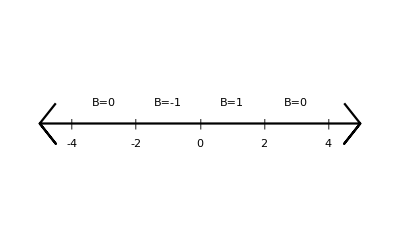

```mathematica
ListPlot[{{-4.5,0.2},{-5,0},{-4.5,-0.2},{-5,0},{5,0},{4.5,-0.2},{5,0},{4.5,0.2}},Joined->True,Axes-> False,PlotStyle-> Black,PlotRange->{{-5.1,5.1},{-1,1}},
BaseStyle->18,
Epilog->{Inset["4",{4,-0.2}],Inset["2",{2,-0.2}],Inset["0",{0,-0.2}],Inset["-2",{-2,-0.2}],Inset["-4",{-4,-0.2}],
Inset["|",{-4,0}],Inset["|",{-2,0}],Inset["|",{0,0}],Inset["|",{2,0}],Inset["|",{4,0}],Inset["B=0",{3,0.2}],
Inset["B=0",{-3,0.2}],Inset["B=-1",{-1,0.2}],Inset["B=1",{1,0.2}]}]
```

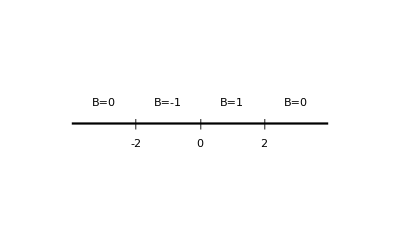

```mathematica
A=ListPlot[{{-4,0},{4,0}},Joined->True,Axes-> False,PlotStyle-> Black,PlotRange->{{-5.1,5.1},{-1,1}},
BaseStyle->18,
Epilog->{Inset["2",{2,-0.2}],Inset["0",{0,-0.2}],Inset["-2",{-2,-0.2}],Inset["|",{-2,0}],Inset["|",{0,0}],Inset["|",{2,0}],Inset["B=0",{3,0.2}],
Inset["B=0",{-3,0.2}],Inset["B=-1",{-1,0.2}],Inset["B=1",{1,0.2}]}]
```

```mathematica
B1=Graphics[{Black,Arrow[BSplineCurve[{{3,0},{4,0},{4.1,0}}]]}]
```

-Graphics-

```mathematica
B2=Graphics[{Black,Arrow[BSplineCurve[{{-3,0},{-4,0},{-4.1,0}}]]}]
```

-Graphics-

```mathematica
Show[A,B1,B2]
```

-Graphics-